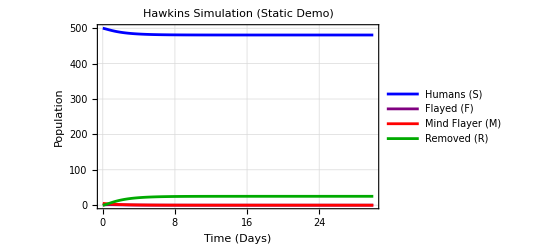

Generating Bifurcation Diagram...

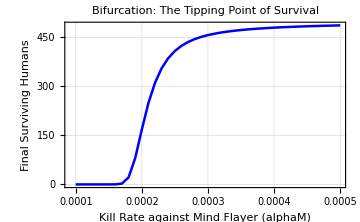

-Graphics-

Generating Ensemble Sensitivity Plot...

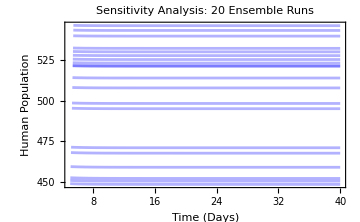

```mathematica
(*PART 1:THE MIND FLAYER MODEL (SFMR System)*)
(*Initialise the environment*)Clear["Global`*"]

(*1. Define the System of Differential Equations*)
(*s:Humans,f:Flayed,m:Mind Flayer,r:Removed*)
equations={(*HUMANS:Infections (by M) and Deaths (by F)*)s'[t]==-beta*s[t]*m[t]-delta*s[t]*f[t],(*FLAYED:Created by M,Killed by Humans*)f'[t]==beta*s[t]*m[t]-alphaF*s[t]*f[t],(*MIND FLAYER:Grows,Killed by Humans*)m'[t]==rho*m[t]-alphaM*s[t]*m[t],(*REMOVED:Sum of all casualties*)r'[t]==delta*s[t]*f[t]+alphaF*s[t]*f[t]+alphaM*s[t]*m[t],(*Initial Conditions*)s[0]==500,f[0]==0,m[0]==5,r[0]==0};

(*2. Define Parameters*)
paramsStranger={beta->0.002,(*Base Infection Rate*)delta->0.005,(*Base Flayed Lethality*)alphaF->0.005,(*Humans killing Flayed*)alphaM->0.00125,(*Humans killing Mind Flayer*)rho->0.1        (*Mind Flayer Regen*)};
tMax=30;

(*3. Solve Numerically*)
(*Use Clear to ensure no variable collision*)
Clear[solStranger,s,f,m,r,t];
solStranger=NDSolve[equations/. paramsStranger,{s,f,m,r},{t,0,tMax}];

(*4. Plot Time Evolution*)
Plot[Evaluate[{s[t],f[t],m[t],r[t]}/. solStranger],{t,0,tMax},PlotStyle->{Blue,Purple,Red,Darker[Green]},PlotLegends->{"Humans (S)","Flayed (F)","Mind Flayer (M)","Removed (R)"},PlotLabel->"Hawkins Simulation (Static Demo)",AxesLabel->{"Time (Days)","Population"},PlotTheme->"Detailed"]



(*PART 2:Tunable Combat Simulator*)

Manipulate[Module[{sol},(*Dynamic Solution*)sol=NDSolve[{S'[t]==-b*S[t]*M[t]-d*S[t]*F[t],F'[t]==b*S[t]*M[t]-aF*S[t]*F[t],M'[t]==rM*M[t]-aM*S[t]*M[t],R'[t]==d*S[t]*F[t]+aF*S[t]*F[t]+aM*S[t]*M[t],S[0]==Sstart,F[0]==Fstart,M[0]==Mstart,R[0]==0},{S,F,M,R},{t,0,time}];
Column[{(*Main Time Series*)Plot[Evaluate[{S[t],F[t],M[t],R[t]}/. sol],{t,0,time},PlotRange->{{0,time},All},PlotStyle->{Blue,Purple,Red,Darker[Green]},PlotLegends->{"Humans","Flayed","Mind Flayer","Removed"},ImageSize->450,AxesLabel->{"Days","Pop"},PlotLabel->"Battle Simulator"],(*Simple Status*)Row[{Style["Current Sim Days: ",Bold],time}]}]],(*---CONTROLS---*)Style["Initial Populations",Bold],{{Sstart,500,"Starting Humans"},10,1000,10},{{Fstart,0,"Starting Flayed"},0,100,1},{{Mstart,1,"Starting Mind Flayers"},1,10,1},Delimiter,Style["Base Attributes",Bold],{{b,0.002,"Base Infection Rate"},0.0,0.01},{{d,0.005,"Base Flayed Aggression"},0.0,0.02},{{aF,0.005,"Human Resistance vs Flayed"},0.0,0.02},{{aM,0.00125,"Human Resistance vs MF"},0.0,0.01},{{rM,0.1,"Mind Flayer Regen"},0.0,0.5},Delimiter,{{time,30,"Simulation Days"},10,100}]



(*PART 3:BIFURCATION DIAGRAM (Survival Analysis)*)
(*Vary alphaCheck (Human ability to kill Mind Flayer) and check final Human population*)

Print["Generating Bifurcation Diagram..."];
ListLinePlot[Table[Module[{solBif,finalHumans,s,f,m,r,t},(*Clear variables locally to prevent'non-numerical derivative' errors*)Clear[s,f,m,r,t];
solBif=NDSolve[{s'[t]==-0.002*s[t]*m[t]-0.005*s[t]*f[t],f'[t]==0.002*s[t]*m[t]-0.005*s[t]*f[t],(*REPAIR:Renamed aM_val to alphaCheck to avoid underscore error*)m'[t]==0.1*m[t]-alphaCheck*s[t]*m[t],r'[t]==0.005*s[t]*f[t]+0.005*s[t]*f[t]+alphaCheck*s[t]*m[t],s[0]==500,f[0]==0,m[0]==1,r[0]==0},{s,f,m,r},{t,0,100}];
(*Get Human population at t=100*)finalHumans=First[Evaluate[s[100]/. solBif]];
{alphaCheck,finalHumans}],{alphaCheck,0.0001,0.0005,0.00001} (*Scanning alphaM from weak to strong*)],PlotStyle->{Thickness[0.005],Blue},Frame->True,FrameLabel->{"Kill Rate against Mind Flayer (alphaM)","Final Surviving Humans"},PlotLabel->"Bifurcation: The Tipping Point of Survival",GridLines->Automatic,ImageSize->Medium]


(*PART 4:VECTOR FIELD/STREAM PLOT*)
(*Visualizing the'Flow' of battle in the Human vs Mind Flayer plane*)
Clear[S,M];

StreamPlot[{(*dS/dt with fixed parameters*)-0.002*S*M-0.005*S*5,(*Assuming~5 Flayed constant for projection*)(*dM/dt*)0.1*M-0.00025*S*M (*Weak Humans scenario*)},{S,0,600},{M,0,100},StreamStyle->"Line",StreamColorFunction->"Rainbow",FrameLabel->{"Humans (S)","Mind Flayer (M)"},PlotLabel->"Phase Space Flow (Vector Field)",ImageSize->Medium]


(*PART 5:SENSITIVITY ENSEMBLE SIMULATION*)
(*Simulating 20 runs with random noise in initial Human population*)

Print["Generating Ensemble Sensitivity Plot..."];
Show[Table[Module[{solEnsemble,noisyS0,s,f,m,r,t},Clear[s,f,m,r,t];
(*Vary Initial Humans by+/-10% random noise*)noisyS0=500*RandomReal[{0.9,1.1}];
solEnsemble=NDSolve[{s'[t]==-0.002*s[t]*m[t]-0.005*s[t]*f[t],f'[t]==0.002*s[t]*m[t]-0.005*s[t]*f[t],m'[t]==0.1*m[t]-0.00125*s[t]*m[t],r'[t]==0.005*s[t]*f[t]+0.005*s[t]*f[t]+0.00125*s[t]*m[t],s[0]==noisyS0,f[0]==0,m[0]==1,r[0]==0},{s,f,m,r},{t,0,40}];
Plot[Evaluate[s[t]/. solEnsemble],{t,0,40},PlotStyle->Directive[Opacity[0.3],Blue]]],{20} (*Run 20 times*)],PlotRange->All,Frame->True,FrameLabel->{"Time (Days)","Human Population"},PlotLabel->"Sensitivity Analysis: 20 Ensemble Runs",ImageSize->Medium]
```